```mathematica
loss[x_, y_, z_]:=x E^y+z
range={-1, 1, 0.1};

Manipulate[ContourPlot3D[loss[x, y, z]==a, {x, -1, 1},{y,-1,1},{z,-1,1}, Mesh->None], {a,-3,3}]
```

```mathematica
d=0.0001;
temp=0.03;
```

```mathematica
varsAndBounds={{x, -1, 1, 1}, {y, -1, 2, 1}, {z, -1, 3, 1}};
plots={};
indices=Flatten[Table@@Prepend[varsAndBounds, varsAndBounds[[All, 1]]], Length[varsAndBounds]-1];
Last[AppendTo[plots, ListPointPlot3D[indices]]]
```

-Graphics3D-

```mathematica
Table[
gradients=(loss@@(#+d*IdentityMatrix[Length[varsAndBounds]])-loss@@#)/d&/@indices;
indices=indices-temp*gradients;
indices=Table[Clip[#[[i]], varsAndBounds[[i, 2;;3]]],{i, Length[varsAndBounds]}]&/@indices;
Last[AppendTo[plots, ListPointPlot3D[indices, PlotRange->varsAndBounds[[All, 2;;3]]]]], {i, 100}];
```

```mathematica
ListAnimate[plots]
```

```mathematica
indices[[Position[loss@@@indices, Min[loss@@@indices]][[1, 1]]]]
```

{-1,2,-1}

```mathematica
gridDescentMinimize[loss_, varsAndBounds_, iters_:20, tempInput_:None, d_:0.0001]:=Module[
{temp=If[tempInput==None, Mean[varsAndBounds[[All, 4]]]/10,tempInput],
indices=Flatten[Table@@Prepend[varsAndBounds, varsAndBounds[[All, 1]]], Length[varsAndBounds]-1],
gradients, progress=PrintTemporary["0% Complete"]}, 
Table[
gradients=(loss@@(#+d*IdentityMatrix[Length[varsAndBounds]])-loss@@#)/d&/@indices;
indices=indices-temp*gradients;
indices=Table[Clip[#[[i]], varsAndBounds[[i, 2;;3]]],{i, Length[varsAndBounds]}]&/@indices;
NotebookDelete[progress];progress=PrintTemporary[ToString[Round[100*iter/iters]]<>"% Complete"];
, {iter, iters}];
indices[[Position[loss@@@indices, Min[loss@@@indices]][[1, 1]]]]
]
```

```mathematica
loss[x_, y_, z_]:=x E^y+z
varsAndBounds={{x, -1, 1, 1}, {y, -1, 2, 1}, {z, -1, 3, 1}};
gridDescentMinimize[loss, varsAndBounds, 200]
```

$Aborted

```mathematica
NMinimize[Join[{loss[x, y,z]}, (#2<=#1<=#3)&@@@varsAndBounds], varsAndBounds[[All, 1]]]
```

{-8.38906,{x→-1.,y→2.,z→-1.}}

```mathematica
gridDescentPlotMinimize[loss_, varsAndBounds_, iters_:20, tempInput_:None, d_:0.0001]:=
Module[
{temp=If[tempInput===None, Mean[varsAndBounds[[All, 4]]]/10,tempInput],
indices=Flatten[Table@@Prepend[varsAndBounds, varsAndBounds[[All, 1]]], Length[varsAndBounds]-1],
gradients, progress=PrintTemporary["0% Complete"],iHist={},
plotFunc=Switch[Length[varsAndBounds],
1,ListLinePlot[Transpose[#[[All, All, 1]]],PlotRange->varsAndBounds[[1, 2;;3]]]&,
2,ListAnimate[Table[NotebookDelete[progress];progress=PrintTemporary[ToString[Round[100*hi/Length[#]]]<>"% Plotted"]; ListPlot[#[[hi]], PlotRange->varsAndBounds[[All, 2;;3]]], {hi, Length[#]}]]&,
3,ListAnimate[Table[NotebookDelete[progress];progress=PrintTemporary[ToString[Round[100*hi/Length[#]]]<>"% Plotted"];ListPointPlot3D[#[[hi]], PlotRange->varsAndBounds[[All, 2;;3]]], {hi, Length[#]}]]&,
_,"No Plot"&
]
},
iHist={indices};
Table[
gradients=(loss@@(#+d*IdentityMatrix[Length[varsAndBounds]])-loss@@#)/d&/@indices;
indices=indices-temp*gradients;
indices=Table[Clip[#[[i]], varsAndBounds[[i, 2;;3]]],{i, Length[varsAndBounds]}]&/@indices;
AppendTo[iHist, indices];
NotebookDelete[progress];progress=PrintTemporary[ToString[Round[100*iter/iters]]<>"% Minimized"];
, {iter, iters}];
Labeled[plotFunc[iHist],indices[[Position[loss@@@indices, Min[loss@@@indices]][[1, 1]]]]]
]
```

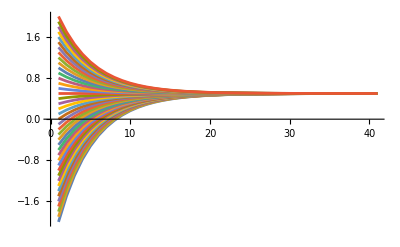
-Graphics-{0.500003}

```mathematica
gridDescentPlotMinimize[(#-0.5)^2&, {{x,-2,2,0.1}}, 40,0.1]
```

```mathematica
gridDescentPlotMinimize[(#1*#2-0.5)^2&, {{x,-2,2,0.1}, {y,-2,2,1}}, 100,0.01]
```

{-2,-0.24999}

```mathematica
gridDescentPlotMinimize[(#1*#2*#3-0.5)^2&, {{x,-1,1,0.1}, {y,-1,1,0.1}, {z,-1,1,0.1}}, 1000]
```

$Aborted